#### functions; must be LOADED IN

#### general

```mathematica
V[r_,Ak_]:=Sum[Ak⟦k⟧(Rak⟦k⟧-r)^3 HeavisideTheta[Rak⟦k⟧-r],{k,Rak//Length}]
Φ[r_,Bk_]:=Sum[Bk⟦k⟧(Rbk⟦k⟧-r)^3 HeavisideTheta[Rbk⟦k⟧-r],{k,Rbk//Length}]
ρ[Bk_]:=∑_(j=1)^n Φ[nR⟦j⟧,Bk]
f[ρ_]:=Sqrt[ρ]

Ecohesion[Ak_,Bk_]:=-1/2∑_(j=1)^n V[nR⟦j⟧,Ak]+f[ρ[Bk]]
Evacancy[Ak_,Bk_]:=Ecohesion[Ak,Bk]-f[ρ[Bk]]+Dρ[Bk]ρ[Bk]

(* first derivatives *)
Dρ[Bk_]:=D[f[ρ],ρ]/.ρ->ρ[Bk]
DV[j_Integer,Ak_]:=D[V[r,Ak],r]/.r->nR⟦j⟧
DΦ[j_Integer,Bk_]:=D[Φ[r,Bk],r]/.r->nR⟦j⟧

(* second derivatives *)
Dρ2[Bk_]:=D[f[ρ],{ρ,2}]/.ρ->ρ[Bk]
DV2[j_Integer,Ak_]:=D[V[r,Ak],{r,2}]/.r->nR⟦j⟧
DΦ2[j_Integer,Bk_]:=D[Φ[r,Bk],{r,2}]/.r->nR⟦j⟧

(* auxiliary definitions *)
R2[j_Integer,α_Integer,β_Integer]:=(R⟦j,α⟧R⟦j,β⟧)/nR⟦j⟧
R4[j_Integer,α_Integer,β_Integer,γ_Integer,δ_Integer]:=(R⟦j,α⟧R⟦j,β⟧R⟦j,γ⟧R⟦j,δ⟧)/nR⟦j⟧^2

(* standard mapping of 2 indices on 1, e.g. Ref. "Theory of dislocations" Hirth and Lothe *)
map[i_Integer]:=Switch[i,
1,{1,1},2,{2,2},3,{3,3},4,{2,3},5,{3,1},6,{1,2},7,{3,2},8,{1,3},9,{2,1},_,(Print["Mapping not possible! Aborting"];Abort[];)];

(* parameters for fitting *)
Akn:=Array[AA,Length[Ak]];
Bkn:=Array[BB,Length[Bk]];
```

#### hcp

```mathematica
(* stress tensor *)
σhcp[α_Integer,β_Integer,Ak_,Bk_] :=(1/2∑_(j=1)^n R2[j,α,β]DV[j,Ak]-Dρ[Bk]∑_(j=1)^n R2[j,α,β]DΦ[j,Bk])/Ω

(* elastic constants *)
Chcp[α_Integer,β_Integer,γ_Integer,δ_Integer,Ak_,Bk_]:=(1/2∑_(j=1)^n R4[j,α,β,γ,δ](DV2[j,Ak]-DV[j,Ak]/nR⟦j⟧)-(Dρ[Bk]∑_(j=1)^n R4[j,α,β,γ,δ](DΦ2[j,Bk]-DΦ[j,Bk]/nR⟦j⟧)+Dρ2[Bk]∑_(j=1)^n R2[j,α,β]DΦ[j,Bk]∑_(j=1)^n R2[j,γ,δ]DΦ[j,Bk]))/Ω

Chcp[α_Integer,β_Integer,Ak_,Bk_]:=Chcp[map[α]⟦1⟧,map[α]⟦2⟧,map[β]⟦1⟧,map[β]⟦2⟧,Ak,Bk]

(* follwoing functions for efficient fitting *)
rule[Ak_,Bk_]:=(#⟦1⟧->#⟦2⟧&/@({Join[Akn,Bkn],Join[Ak,Bk]}ᵀ));
Ecoh[Ak_,Bk_]:=EcohAknBkn/.rule[Ak,Bk]
Evac[Ak_,Bk_]:=EvacAknBkn/.rule[Ak,Bk]
σhcp11[Ak_,Bk_]:=σhcp11AknBkn/.rule[Ak,Bk]
σhcp33[Ak_,Bk_]:=σhcp33AknBkn/.rule[Ak,Bk]
Chcp11[Ak_,Bk_]:=Chcp11AknBkn/.rule[Ak,Bk]
Chcp12[Ak_,Bk_]:=Chcp12AknBkn/.rule[Ak,Bk]
Chcp13[Ak_,Bk_]:=Chcp13AknBkn/.rule[Ak,Bk]
Chcp33[Ak_,Bk_]:=Chcp33AknBkn/.rule[Ak,Bk]
Chcp44[Ak_,Bk_]:=Chcp44AknBkn/.rule[Ak,Bk]
```

#### utilities

```mathematica
fccCell[a_Real:1.]:=a/2{{0,1,1},{1,0,1},{1,1,0}};
bccCell[a_Real:1.]:=a/2{{-1,1,1},{1,-1,1},{1,1,-1}};scCell[a_Real:1.]:=a{{1,0,0},{0,1,0},{0,0,1}};
hcpCell[a_Real:1.,cBya_Real:1.5]:=a{{1,0,0},{1/2,3^(1/2)/2,0},{0,0,cBya}}
hcpCell[a_,cBya_]:=a{{1,0,0},{1/2,3^(1/2)/2,0},{0,0,cBya}}
hcpCoordsRel={{0,0,0},{1/3,1/3,1/2}};

neighborsList[cell_List,radius_]:=neighborsList[cell,{{0,0,0}},1,radius]

neighborsList[cell_List,basisRel_List,atomNr_Integer,radius_]:=Module[
{
delta=10^-4,sphereCovered=False,n=0,
neighborsList={},checkAtom,distance,notInSphere,permList,permsDone={}
},
(
While[!sphereCovered,
notInSphere=0; 
permList=Complement[Tuples[Range[-n,n],{3}],permsDone];
Do[
checkAtom=permList⟦i⟧.cell+basisRel⟦j⟧.cell;
distance=Norm[basisRel⟦atomNr⟧.cell-checkAtom];
If[distance<radius,AppendTo[neighborsList,checkAtom],notInSphere++];
,{i,permList//Length},{j,basisRel//Length}];
If[Length[basisRel]Length[permList]==notInSphere,sphereCovered=True];
permsDone=Join[permsDone,permList];
n++;
];
neighborsList//Rest
)]
```

```mathematica
SetDirectory["/home/grabowski/newSPHInX_sources/sphinx/src/share/SPHInX/potentials_eam/"];
```

#### Mo Ackland Ref. G.J.Ackland and R.Thetford, Phil.Mag.A, 56, 15 (1987)

```mathematica
str="Mo";
eam=Import[str<>"/"<>str<>".AT1.fs","Table"];
```

```mathematica
header=eam⟦1;;6⟧;
eam=eam⟦7;;-1⟧;
eam=eam//Flatten;
```

```mathematica
Nrho=header⟦5,1⟧;
drho=header⟦5,2⟧;
Nr=header⟦5,3⟧;
dr=header⟦5,4⟧;
```

```mathematica
emb=Table[{(i-1)drho,eam⟦i⟧},{i,Nrho}];
rho=Table[{(i-1)dr,eam⟦i+Nrho⟧},{i,Nr}];
pair=Table[{(i-1)dr,eam⟦i+Nrho+Nr⟧},{i,Nr}];
Do[pair⟦i,2⟧/=pair⟦i,1⟧,{i,2,pair//Length}];
pair⟦1,2⟧=pair⟦2,2⟧;
```

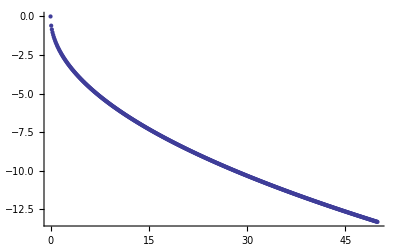

```mathematica
ListPlot[emb⟦1;;-1⟧,PlotRange->Automatic]
```

```mathematica
a0=3.8;
radius=2a0;
rhoInt[r_]:=If[r<Last[rho]⟦1⟧,Interpolation[rho][r],0];
nRSmallALat=Norm/@neighborsList[bccCell[.8a0],radius];
n=Length[nRSmallALat];
Table[{nRSmallALat⟦j⟧,rhoInt[nRSmallALat⟦j⟧]},{j,n}];
∑_(j=1)^n rhoInt[nRSmallALat⟦j⟧]
```

24.5046

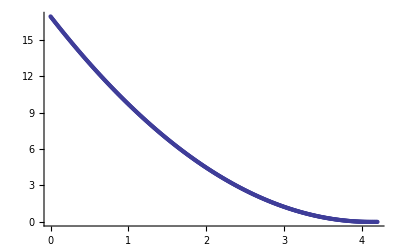

```mathematica
ListPlot[rho⟦1;;-1⟧]
```

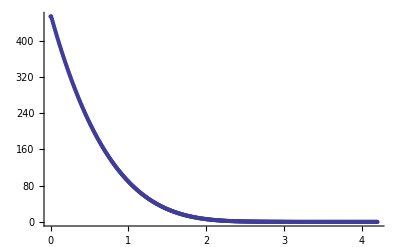

```mathematica
ListPlot[pair⟦1;;-1⟧,PlotRange->All]
```

```mathematica
Export[str<>"/"<>str<>"_AT_pair",pair,"Table"]
Export[str<>"/"<>str<>"_AT_rho",rho,"Table"]
Export[str<>"/"<>str<>"_AT_emb",emb,"Table"]
```

Mo/Mo_AT_pair

Mo/Mo_AT_rho

Mo/Mo_AT_emb

#### Cu Ackland Ref. web; equivalent with Cu Ackland from below

```mathematica
str="Cu";
eam=Import[str<>"/"<>str<>"_Ackland.eam.fs","Table"];
```

```mathematica
header=eam⟦1;;6⟧;
eam=eam⟦7;;-1⟧;
eam=eam//Flatten;
```

```mathematica
Nrho=header⟦5,1⟧;
drho=header⟦5,2⟧;
Nr=header⟦5,3⟧;
dr=header⟦5,4⟧;
```

```mathematica
emb=Table[{(i-1)drho,eam⟦i⟧},{i,Nrho}];
rho=Table[{(i-1)dr,eam⟦i+Nrho⟧},{i,Nr}];
pair=Table[{(i-1)dr,eam⟦i+Nrho+Nr⟧},{i,Nr}];
Do[pair⟦i,2⟧/=pair⟦i,1⟧,{i,2,pair//Length}];
pair⟦1,2⟧=pair⟦2,2⟧;
```

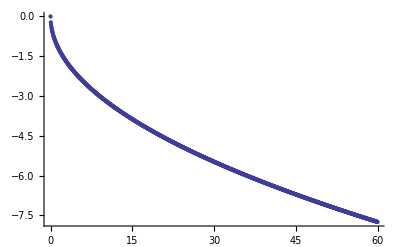

```mathematica
ListPlot[emb⟦1;;1200⟧,PlotRange->Automatic]
```

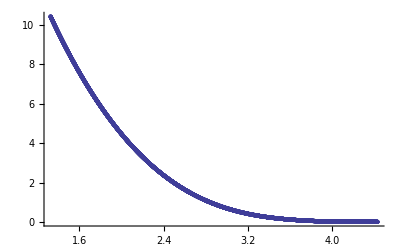

```mathematica
ListPlot[rho⟦3000;;-1⟧]
```

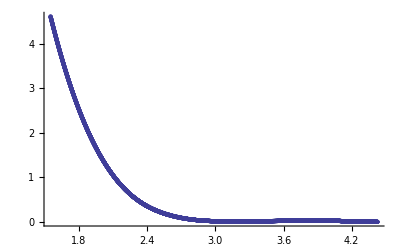

```mathematica
ListPlot[pair⟦3500;;-1⟧]
```

```mathematica
Export[str<>"/"<>str<>"_Ackland2_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Ackland2_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Ackland2_emb",emb,"Table"]
```

Cu/Cu_Ackland2_pair

Cu/Cu_Ackland2_rho

Cu/Cu_Ackland2_emb

#### Ru Mendelev Ref. http://www.ctcms.nist.gov/potentials/Download/Ru-MIM/Ru.eam.fs

```mathematica
str="Ru";
eam=Import[str<>"/"<>str<>"_Mendelev.eam.fs","Table"];
```

```mathematica
header=eam⟦1;;6⟧;
eam=eam⟦7;;-1⟧;
eam=eam//Flatten;
```

```mathematica
Nrho=header⟦5,1⟧;
drho=header⟦5,2⟧;
Nr=header⟦5,3⟧;
dr=header⟦5,4⟧;
```

```mathematica
emb=Table[{(i-1)drho,eam⟦i⟧},{i,Nrho}];
rho=Table[{(i-1)dr,eam⟦i+Nrho⟧},{i,Nr}];
pair=Table[{(i-1)dr,eam⟦i+Nrho+Nr⟧},{i,Nr}];
Do[pair⟦i,2⟧/=pair⟦i,1⟧,{i,2,pair//Length}];
pair⟦1,2⟧=pair⟦2,2⟧;
```

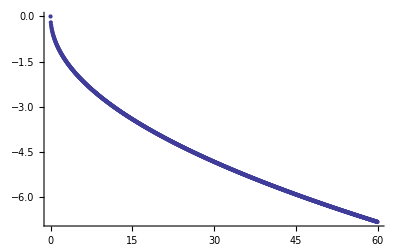

```mathematica
ListPlot[emb⟦1;;1200⟧,PlotRange->Automatic]
```

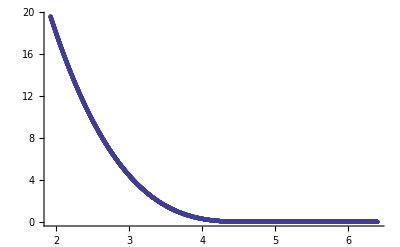

```mathematica
ListPlot[rho⟦3000;;-1⟧]
```

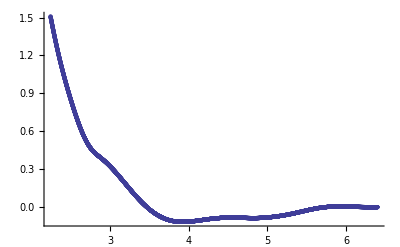

```mathematica
ListPlot[pair⟦3500;;-1⟧]
```

```mathematica
Export[str<>"/"<>str<>"_Mendelev_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Mendelev_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Mendelev_emb",emb,"Table"]
```

Ru/Ru_Mendelev_pair

Ru/Ru_Mendelev_rho

Ru/Ru_Mendelev_emb

#### Fe Ackland Ref. Ackland, Bacon, Calder, Harry, Phil. Mag. A 75 (1997) 713

```mathematica
str="Fe";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Ackland.dat"]//Flatten;
```

```mathematica
{a0,Ec,Ev,σ11,σ33,C11,C12,C44}=prop;

Ak=par⟦1;;6⟧/a0^3;
Bk=par⟦7;;8⟧/a0^3;
Rak=a0 par⟦9;;14⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Rbk=a0 par⟦15;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=bccCell[a0];
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧;
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
(*{σ11,σbcc[1,1,Ak,Bk]}
{σ33,σbcc[3,3,Ak,Bk]}
{C11,Cbcc[1,1,Ak,Bk]}
{C12,Cbcc[1,2,Ak,Bk]}
{C44,Cbcc[4,4,Ak,Bk]}*)
```

{1.89,1.84}

{4.316,4.316}

{23.5419,24.5223}

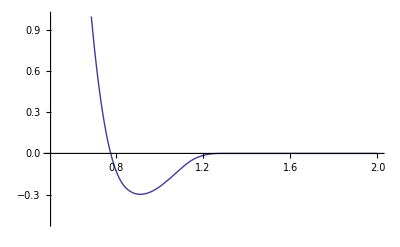

```mathematica
Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2},PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[bccCell[0.8a0],radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=500;
drho=0.05//N;
```

43.8745

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

11467

11467

10001

```mathematica
Export[str<>"/"<>str<>"_Ackland_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Ackland_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Ackland_emb",emb,"Table"]
```

Fe/Fe_Ackland_pair

Fe/Fe_Ackland_rho

Fe/Fe_Ackland_emb

#### Cu Ackland Ref. Ackland, et al., Phil. Mag. A 75 (1997) 713 & Ref. Ackland, et al., Phil. Mag. A 56 (1987) 735

```mathematica
str="Cu";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Ackland.dat"]//Flatten;
```

```mathematica
{a0,Ec,Ev,σ11,σ33,C11,C12,C44,γ,α}=prop;

Ak=par⟦1;;6⟧/a0^3;
Bk=par⟦7;;8⟧/a0^3;
Rak=a0 par⟦9;;14⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Rbk=a0 par⟦15;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=fccCell[a0];
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧;
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{α,V[2a0/3^(1/2),Ak]}
(*{σ11,σbcc[1,1,Ak,Bk]}
{σ33,σbcc[3,3,Ak,Bk]}
{C11,Cbcc[1,1,Ak,Bk]}
{C12,Cbcc[1,2,Ak,Bk]}
{C44,Cbcc[4,4,Ak,Bk]}*)
```

{1.17,1.17158}

{3.518,3.51935}

{22.0524,22.0481}

{0.01,0.00998628}

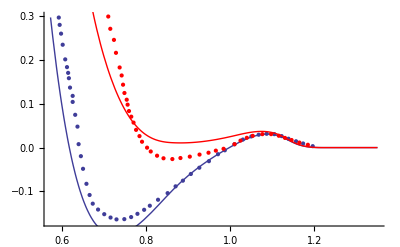

```mathematica
fromAckland=Import[str<>"/EffectivePotential_fromAckland.dat"];
fromAckland2=Import[str<>"/Potential_fromAckland.dat"];
Show[
ListPlot[fromAckland],Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,1.35}],
ListPlot[fromAckland2,PlotStyle->Red],Plot[{V[a0 r ,Ak],ϕ[r]},{r,0.5,1.35},PlotStyle->{Red,Dashed}]
,PlotRange->{-.17,.3},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[fccCell[0.8a0],radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=200;
drho=.02//N;
```

59.0514

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

14461

14461

10001

```mathematica
Export[str<>"/"<>str<>"_Ackland_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Ackland_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Ackland_emb",emb,"Table"]
```

Cu/Cu_Ackland_pair

Cu/Cu_Ackland_rho

Cu/Cu_Ackland_emb

#### Ag Ackland Ref. Ackland, Tichy, Vitek, Finnis, Phil. Mag. A 56 (1987) 735

```mathematica
str="Ag";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Ackland.dat"]//Flatten;
```

```mathematica
{a0,Ec,Ev,σ11,σ33,C11,C12,C44,γ,α}=prop;

Ak=par⟦1;;6⟧/a0^3;
Bk=par⟦9;;10⟧/a0^3;
Rak=a0 par⟦11;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Rbk=a0 par⟦7;;8⟧+10^-7; (* to avoid HeavisideTheta[0] *)

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=fccCell[a0];
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧;
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{α,V[2a0/3^(1/2),Ak]}
(*{σ11,σbcc[1,1,Ak,Bk]}
{σ33,σbcc[3,3,Ak,Bk]}
{C11,Cbcc[1,1,Ak,Bk]}
{C12,Cbcc[1,2,Ak,Bk]}
{C44,Cbcc[4,4,Ak,Bk]}*)
```

{1.,1.00044}

{2.967,2.96744}

{15.4764,15.4764}

{0.007,0.00699966}

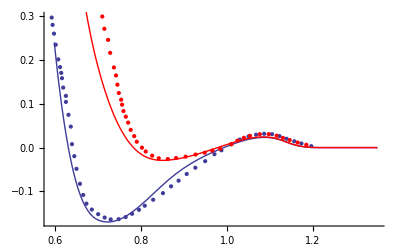

```mathematica
(* WARNING comparing to effective potential of Cu *)
fromAckland=Import["Cu/EffectivePotential_fromAckland.dat"];
fromAckland2=Import["Cu/Potential_fromAckland.dat"];
Show[
ListPlot[fromAckland],Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,1.35}],
ListPlot[fromAckland2,PlotStyle->Red],Plot[V[a0 r ,Ak],{r,0.5,1.35},PlotStyle->{Red}]
,PlotRange->{-.17,.3},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[fccCell[0.8a0],radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=200;
drho=.02//N;
```

50.501

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

16345

16345

10001

```mathematica
Export[str<>"/"<>str<>"_Ackland_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Ackland_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Ackland_emb",emb,"Table"]
```

Ag/Ag_Ackland_pair

Ag/Ag_Ackland_rho

Ag/Ag_Ackland_emb

#### Ti Ackland Ref. G.J.Ackland, Phil.Mag.A, 66, 917. (1992) FITTED TO FCC

```mathematica
str="Ti";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Ackland.dat"]//Flatten;
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66,a0fcc,Evfcc}=prop;

Ak=par⟦1;;6⟧/a0fcc^3;
Bk=par⟦7;;8⟧/a0fcc^3;
Rak=a0fcc par⟦9;;14⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Rbk=a0fcc par⟦15;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)

cell=fccCell[a0fcc];
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧;
radius=2a0fcc; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Evfcc,Evacancy[Ak,Bk]}
```

{1.4,1.39081}

Compare to hcp values

```mathematica
ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
```

{1.55,1.3401}

{4.85,4.85054}

{43.56,49.2926}

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[fccCell[0.8a0fcc],radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=500;
drho=.05//N;
```

100.737

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

11805

11805

10001

```mathematica
Export[str<>"/"<>str<>"_Ackland_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Ackland_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Ackland_emb",emb,"Table"]
```

Ti/Ti_Ackland_pair

Ti/Ti_Ackland_rho

Ti/Ti_Ackland_emb

#### Ti Vitek Ref. Igarashi, Khantha, and Vitek, Phil. Mag. B 63 (1991) 603

```mathematica
str="Ti";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Vitek.dat"]//Flatten;
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66,a0fcc,Evfcc}=prop;

Rak=a0 par⟦1;;6⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Ak=par⟦7;;12⟧;
Rbk=a0 par⟦13;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Bk=par⟦17;;20⟧;

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
```

{1.55,1.54997}

{4.85,4.85031}

{43.56,43.5688}

{0,0.0000307889}

{0,0.0000124596}

{1.0992,1.10478}

{0.5424,0.542375}

{0.4263,0.426732}

{1.1891,1.19074}

{0.3171,0.317543}

{0.2812,0.281201}

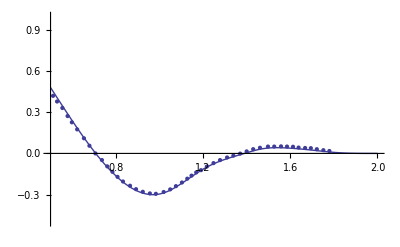

```mathematica
fromVitek=Import[str<>"/EffectivePotential_fromVitek.dat"];
Show[ListPlot[fromVitek],Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2}],PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=2000;
drho=.2//N;
```

1605.27

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

11805

11805

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_emb",emb,"Table"]
```

Ti/Ti_Vitek_pair

Ti/Ti_Vitek_rho

Ti/Ti_Vitek_emb

#### own fitting

```mathematica
EcohAknBkn=Ecohesion[Akn,Bkn];
EvacAknBkn=Evacancy[Akn,Bkn];
σhcp11AknBkn=σhcp[1,1,Akn,Bkn];
σhcp33AknBkn=σhcp[3,3,Akn,Bkn];
Chcp11AknBkn=Chcp[1,1,Akn,Bkn];
Chcp12AknBkn=Chcp[1,2,Akn,Bkn];
Chcp13AknBkn=Chcp[1,3,Akn,Bkn];
Chcp33AknBkn=Chcp[3,3,Akn,Bkn];
Chcp44AknBkn=Chcp[4,4,Akn,Bkn];
```

```mathematica
sol=FindRoot[{Ecoh[Akn,Bkn]==Ec,Evac[Akn,Bkn]==Ev,σhcp11[Akn,Bkn]==σ11,σhcp33[Akn,Bkn]==σ33,Chcp11[Akn,Bkn]==C11,Chcp12[Akn,Bkn]==C12,Chcp13[Akn,Bkn]==C13,Chcp33[Akn,Bkn]==C33,Chcp44[Akn,Bkn]==C44,σhcp[1,2,Akn,Bkn]==0},{Join[Akn,Bkn],Join[.1Ak,.1Bk]}ᵀ]//Chop
```

{AA[1]→-0.412049,AA[2]→1.70512,AA[3]→-0.019473,AA[4]→-4.48367,AA[5]→5.76245,AA[6]→-15.7535,BB[1]→-3.65112,BB[2]→9.15274,BB[3]→-10.0999,BB[4]→60.7688}

```mathematica
(* original Ak Bk *)
Ak
Bk
```

{0.0611882,0.0918677,-0.174851,-0.931018,0.742162,91.371}

{0.0652343,1.24698,-6.28254,607.688}

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Akn,Bkn]/.sol}
{Ec,Ecohesion[Akn,Bkn]/.sol}
{ρ0,ρ[Bkn]/.sol}
{σ11,σhcp[1,1,Akn,Bkn]/.sol}
{σ33,σhcp[3,3,Akn,Bkn]/.sol}
{C11,Chcp[1,1,Akn,Bkn]/.sol}
{C12,Chcp[1,2,Akn,Bkn]/.sol}
{C13,Chcp[1,3,Akn,Bkn]/.sol}
{C33,Chcp[3,3,Akn,Bkn]/.sol}
{C44,Chcp[4,4,Akn,Bkn]/.sol}
{C66,Chcp[6,6,Akn,Bkn]/.sol}
```

{1.55,1.55}

{4.85,4.85}

{43.56,43.56}

{0,-1.00524×10^-15}

{0,6.53409×10^-16}

{1.0992,1.0992}

{0.5424,0.5424}

{0.4263,0.4263}

{1.1891,1.1891}

{0.3171,0.3171}

{0.2812,0.2784}

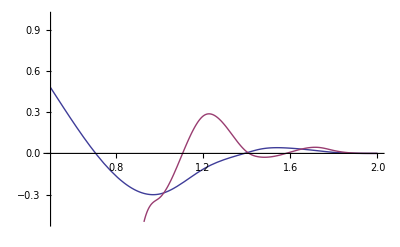

```mathematica
Plot[{
V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],
V[a0 r ,Akn]-2 Dρ[Bkn]Φ[a0 r,Bkn]/.sol
},{r,0.5,2},PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

#### Mg Vitek Ref. Igarashi, Khantha, and Vitek, Phil. Mag. B 63 (1991) 603

```mathematica
str="Mg";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Vitek.dat"]//Flatten;
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66}=prop;

Rak=a0 par⟦1;;6⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Ak=par⟦7;;12⟧;
Rbk=a0 par⟦13;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Bk=par⟦17;;20⟧;

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
```

{0.8,0.810049}

{1.51,1.54408}

{2.0164,2.15523}

{0,2.97128×10^-6}

{0,1.62484×10^-6}

{0.3962,0.396579}

{0.1619,0.161991}

{0.1355,0.135593}

{0.4148,0.41516}

{0.115,0.115094}

{0.1172,0.117294}

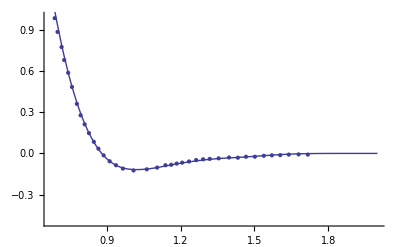

```mathematica
fromVitek=Import[str<>"/EffectivePotential_fromVitek.dat"];
Show[ListPlot[fromVitek],Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2}],PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=1000;
drho=.1//N;
```

239.029

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

12837

12837

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_emb",emb,"Table"]
```

Mg/Mg_Vitek_pair

Mg/Mg_Vitek_rho

Mg/Mg_Vitek_emb

#### own fitting

```mathematica
EcohAknBkn=Ecohesion[Akn,Bkn];
EvacAknBkn=Evacancy[Akn,Bkn];
σhcp11AknBkn=σhcp[1,1,Akn,Bkn];
σhcp33AknBkn=σhcp[3,3,Akn,Bkn];
Chcp11AknBkn=Chcp[1,1,Akn,Bkn];
Chcp12AknBkn=Chcp[1,2,Akn,Bkn];
Chcp13AknBkn=Chcp[1,3,Akn,Bkn];
Chcp33AknBkn=Chcp[3,3,Akn,Bkn];
Chcp44AknBkn=Chcp[4,4,Akn,Bkn];
```

```mathematica
sol=FindRoot[{Ecoh[Akn,Bkn]==Ec,Evac[Akn,Bkn]==Ev,σhcp11[Akn,Bkn]==σ11,σhcp33[Akn,Bkn]==σ33,Chcp11[Akn,Bkn]==C11,Chcp12[Akn,Bkn]==C12,Chcp13[Akn,Bkn]==C13,Chcp33[Akn,Bkn]==C33,Chcp44[Akn,Bkn]==C44,σhcp[1,2,Akn,Bkn]==0},{Join[Akn,Bkn],Join[.1Ak,.1Bk]}ᵀ]//Chop
```

{AA[1]→-3.15065,AA[2]→2.12454,AA[3]→6.38253,AA[4]→0.644733,AA[5]→-33.7124,AA[6]→177.128,BB[1]→-4.64315,BB[2]→12.9126,BB[3]→-13.9822,BB[4]→6.26316}

```mathematica
(* original Ak Bk *)
Ak
Bk
```

{0.0319086,-0.0297906,0.0254509,-0.27641,0.221558,43.1684}

{0.0623314,-0.0656703,-0.365966,62.6316}

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Akn,Bkn]/.sol}
{Ec,Ecohesion[Akn,Bkn]/.sol}
{ρ0,ρ[Bkn]/.sol}
{σ11,σhcp[1,1,Akn,Bkn]/.sol}
{σ33,σhcp[3,3,Akn,Bkn]/.sol}
{C11,Chcp[1,1,Akn,Bkn]/.sol}
{C12,Chcp[1,2,Akn,Bkn]/.sol}
{C13,Chcp[1,3,Akn,Bkn]/.sol}
{C33,Chcp[3,3,Akn,Bkn]/.sol}
{C44,Chcp[4,4,Akn,Bkn]/.sol}
{C66,Chcp[6,6,Akn,Bkn]/.sol}
```

{0.8,0.8}

{1.51,1.51}

{2.0164,2.0164}

{0,-4.57699×10^-15}

{0,-1.44285×10^-15}

{0.3962,0.3962}

{0.1619,0.1619}

{0.1355,0.1355}

{0.4148,0.4148}

{0.115,0.115}

{0.1172,0.11715}

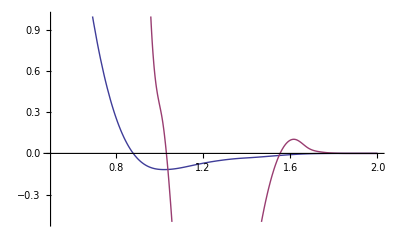

```mathematica
Plot[{
V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],
V[a0 r ,Akn]-2 Dρ[Bkn]Φ[a0 r,Bkn]/.sol
},{r,0.5,2},PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

#### Hf Vitek Ref. Igarashi, Khantha, and Vitek, Phil. Mag. B 63 (1991) 603

```mathematica
str="Hf";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Vitek.dat"]//Flatten;
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66}=prop;

Rak=a0 par⟦1;;6⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Ak=par⟦7;;12⟧;
Rbk=a0 par⟦13;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Bk=par⟦17;;20⟧;

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
```

{2.15,2.15025}

{6.44,6.44001}

{73.6164,73.608}

{0,3.15522×10^-6}

{0,-0.000348363}

{1.1866,1.16792}

{0.465,0.458526}

{0.4089,0.407287}

{1.2759,1.27815}

{0.3745,0.375136}

{0.3608,0.3547}

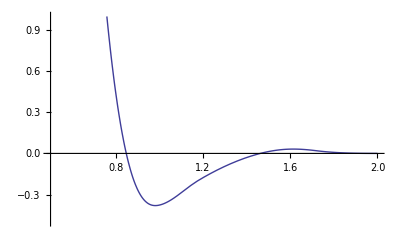

```mathematica
Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2},PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=3000;
drho=.3//N;
```

2074.69

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

12777

12777

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_emb",emb,"Table"]
```

Hf/Hf_Vitek_pair

Hf/Hf_Vitek_rho

Hf/Hf_Vitek_emb

#### Ru Vitek_highT Ref. Igarashi, Khantha, and Vitek, Phil. Mag. B 63 (1991) 603

```mathematica
str="Ru";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Vitek_highT.dat"]//Flatten;
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66}=prop;

Rak=a0 par⟦1;;6⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Ak=par⟦7;;12⟧;
Rbk=a0 par⟦13;;16⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Bk=par⟦17;;20⟧;

ρ0=ρρ0/.Solve[Ev==Ec-f[ρρ0]+D[f[ρρ0],ρρ0]ρρ0,ρρ0]⟦1⟧;
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
```

{2.25,2.24755}

{6.74,6.85229}

{80.6404,84.8144}

{0,0.00366294}

{0,-0.0239065}

{3.597,3.51823}

{1.1684,1.18146}

{1.0442,1.64566}

{3.9977,6.22907}

{1.1803,1.7749}

{1.2143,1.16839}

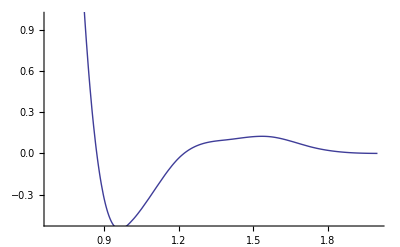

```mathematica
Show[Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2}],PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=10000;
drho=10^0//N;
```

8156.03

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

11005

11005

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_highT_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_highT_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_highT_emb",emb,"Table"]
```

Ru/Ru_Vitek_highT_pair

Ru/Ru_Vitek_highT_rho

Ru/Ru_Vitek_highT_emb

#### own fitting

```mathematica
EcohAknBkn=Ecohesion[Akn,Bkn];
EvacAknBkn=Evacancy[Akn,Bkn];
σhcp11AknBkn=σhcp[1,1,Akn,Bkn];
σhcp33AknBkn=σhcp[3,3,Akn,Bkn];
Chcp11AknBkn=Chcp[1,1,Akn,Bkn];
Chcp12AknBkn=Chcp[1,2,Akn,Bkn];
Chcp13AknBkn=Chcp[1,3,Akn,Bkn];
Chcp33AknBkn=Chcp[3,3,Akn,Bkn];
Chcp44AknBkn=Chcp[4,4,Akn,Bkn];
```

```mathematica
sol=FindRoot[{Ecoh[Akn,Bkn]==Ec,Evac[Akn,Bkn]==Ev,σhcp11[Akn,Bkn]==σ11,σhcp33[Akn,Bkn]==σ33,Chcp11[Akn,Bkn]==C11,Chcp12[Akn,Bkn]==C12,Chcp13[Akn,Bkn]==C13,Chcp33[Akn,Bkn]==C33,Chcp44[Akn,Bkn]==C44,σhcp[1,2,Akn,Bkn]==0},{Join[Akn,Bkn],Join[2Ak,.89Bk]}ᵀ]//Chop
```

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{AA[1]→-43.482,AA[2]→157.904,AA[3]→37.9082,AA[4]→-242.465,AA[5]→91.7993,AA[6]→21.1927,BB[1]→-343.248,BB[2]→1298.48,BB[3]→-1296.31,BB[4]→3244.54}

```mathematica
(* original Ak Bk *)
Ak
Bk
```

{0.133524,-0.397033,0.859001,-2.63029,2.24415,407.477}

{0.509689,1.27029,-13.2145,3645.55}

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Akn,Bkn]/.sol}
{Ec,Ecohesion[Akn,Bkn]/.sol}
{ρ0,ρ[Bkn]/.sol}
{σ11,σhcp[1,1,Akn,Bkn]/.sol}
{σ33,σhcp[3,3,Akn,Bkn]/.sol}
{C11,Chcp[1,1,Akn,Bkn]/.sol}
{C12,Chcp[1,2,Akn,Bkn]/.sol}
{C13,Chcp[1,3,Akn,Bkn]/.sol}
{C33,Chcp[3,3,Akn,Bkn]/.sol}
{C44,Chcp[4,4,Akn,Bkn]/.sol}
{C66,Chcp[6,6,Akn,Bkn]/.sol}
```

{2.25,2.25}

{6.74,6.74}

{80.6404,80.6404}

{0,0.000086124}

{0,-0.000579262}

{3.597,3.59727}

{1.1684,1.20071}

{1.0442,0.712902}

{3.9977,6.35909}

{1.1803,1.16955}

{1.2143,1.19828}

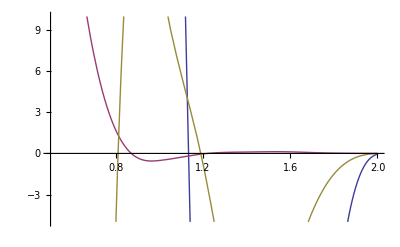

```mathematica
Plot[{
V[a0 r,Akn]/.sol,
V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],
V[a0 r ,Akn]-2 Dρ[Bkn]Φ[a0 r,Bkn]/.sol
},{r,0.5,2},PlotRange->{-5,10},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bkn/.sol]  (* set rhoMax sufficiently beyond this value *)
rhoMax=50000;
drho=5//N;
```

20444.7

```mathematica
pair=Table[{r,V[r,Akn]/.sol},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bkn]/.sol},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
```

```mathematica
emb//Length
```

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_highT_own_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_highT_own_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_highT_own_emb",emb,"Table"]
```

Ru/Ru_Vitek_highT_own_pair

Ru/Ru_Vitek_highT_own_rho

Ru/Ru_Vitek_highT_own_emb

#### Ru Vitek_lowT Ref. Igarashi, Khantha, and Vitek, Phil. Mag. B 63 (1991) 603

```mathematica
str="Ru";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Vitek_lowT.dat"]//Flatten;
```

WARNING: modifying embedding function

```mathematica
f[ρ_]:=Sqrt[ρ](1+A ρ)  (* Ref. Vitek Eq (8) *)
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66}=prop;

Rak=a0 (par⟦1;;7⟧);
Ak=par⟦8;;14⟧;
Rbk=a0 (par⟦15;;19⟧);
Bk=par⟦20;;24⟧;
A=par⟦25⟧;

a0=2.7067; (* this is the lattice constant at which the properties are matched; not the original one; why, I do not know ???? *)

ρ0=1/(2A); (* Ref. Vitek text following Eq. (8) *)
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=3a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
{True,(3ρ[Bk])^-1<A<ρ[Bk]^-1}  (* Ref Vitek text following Eq. (8) *)
```

{2.25,2.25076}

{6.74,6.74067}

{322.562,322.575}

{0,0.00127694}

{0,0.000657437}

{3.597,3.60683}

{1.1684,1.17366}

{1.0442,1.04978}

{3.9977,3.99693}

{1.1803,1.18055}

{1.2143,1.21659}

{True,True}

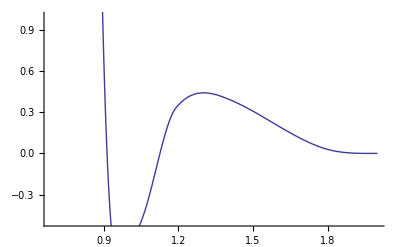

```mathematica
Show[Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2}],PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=5000;
drho=.5//N;
```

3240.05

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

10827

10827

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_lowT_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_lowT_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_lowT_emb",emb,"Table"]
```

Ru/Ru_Vitek_lowT_pair

Ru/Ru_Vitek_lowT_rho

Ru/Ru_Vitek_lowT_emb

#### own fitting Ak Bk

```mathematica
EcohAknBkn=Ecohesion[Akn,Bkn];
EvacAknBkn=Evacancy[Akn,Bkn];
σhcp11AknBkn=σhcp[1,1,Akn,Bkn];
σhcp33AknBkn=σhcp[3,3,Akn,Bkn];
Chcp11AknBkn=Chcp[1,1,Akn,Bkn];
Chcp12AknBkn=Chcp[1,2,Akn,Bkn];
Chcp13AknBkn=Chcp[1,3,Akn,Bkn];
Chcp33AknBkn=Chcp[3,3,Akn,Bkn];
Chcp44AknBkn=Chcp[4,4,Akn,Bkn];
```

```mathematica
ρ2[Ak_,Bk_]:=ρ[Bk];
cond:={{20,Ev,Evac},{20,Ec,Ecoh},{2,ρ0,ρ2},{1000,σ11,σhcp11},{1000,σ33,σhcp33},{100,C11,Chcp11},{100,C12,Chcp12},{100,C13,Chcp13},{100,C33,Chcp33}};
Δ[Ak_,Bk_]:=Sum[cond⟦i,1⟧Abs[cond⟦i,2⟧-cond⟦i,3⟧[Ak,Bk]],{i,cond//Length}]
```

```mathematica
Δ[Ak,Bk]
```

295.905

```mathematica
sol=FindMinimum[Δ[Ak,Bkn],{Bkn,Bk}ᵀ,Method->"ConjugateGradient"]
sol=sol⟦2⟧;
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{275.971,{BB[1]→9.02126,BB[2]→-0.365263,BB[3]→-172.284,BB[4]→335.388,BB[5]→466.906}}

```mathematica
(* original Ak Bk *)
{Ak,Bk}
{Ak,Bkn}/.sol
```

{{1.52066,-0.501081,-24.798,61.6498,50.4874,130.,65.},{9.03267,-0.359251,-172.282,335.389,466.906}}

{{1.52066,-0.501081,-24.798,61.6498,50.4874,130.,65.},{9.02126,-0.365263,-172.284,335.388,466.906}}

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bkn]/.sol}
{Ec,Ecohesion[Ak,Bkn]/.sol}
{ρ0,ρ[Bkn]/.sol}
{σ11,σhcp[1,1,Ak,Bkn]/.sol}
{σ33,σhcp[3,3,Ak,Bkn]/.sol}
{C11,Chcp[1,1,Ak,Bkn]/.sol}
{C12,Chcp[1,2,Ak,Bkn]/.sol}
{C13,Chcp[1,3,Ak,Bkn]/.sol}
{C33,Chcp[3,3,Ak,Bkn]/.sol}
{C44,Chcp[4,4,Ak,Bkn]/.sol}
```

{2.25,1.93988}

{6.74,6.47209}

{322.562,316.347}

{0,0.0825288}

{0,0.0810829}

{3.597,4.15576}

{1.1684,1.32751}

{1.0442,1.21003}

{3.9977,3.9977}

{1.1803,1.19733}

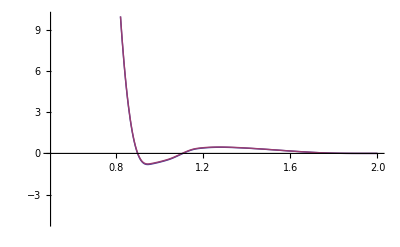

```mathematica
Plot[{
V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],
V[a0 r ,Ak]-2 Dρ[Bkn]Φ[a0 r,Bkn]/.sol
},{r,0.5,2},PlotRange->{-5,10},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bkn/.sol]  (* set rhoMax sufficiently beyond this value *)
rhoMax=50000;
drho=5//N;
```

2814.71

```mathematica
pair=Table[{r,V[r,Ak]/.sol},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bkn]/.sol},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
```

```mathematica
emb//Length
```

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_lowT_own_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_lowT_own_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_lowT_own_emb",emb,"Table"]
```

Ru/Ru_Vitek_lowT_own_pair

Ru/Ru_Vitek_lowT_own_rho

Ru/Ru_Vitek_lowT_own_emb

#### own fitting Rak Rbk

```mathematica
ρ2[Ak_,Bk_]:=ρ[Bk];
σhcp11tmp[Ak_,Bk_]:=σhcp[1,1,Ak,Bk];
σhcp33tmp[Ak_,Bk_]:=σhcp[3,3,Ak,Bk];
Chcp11tmp[Ak_,Bk_]:=Chcp[1,1,Ak,Bk];
Chcp12tmp[Ak_,Bk_]:=Chcp[1,2,Ak,Bk];
Chcp13tmp[Ak_,Bk_]:=Chcp[1,3,Ak,Bk];
Chcp33tmp[Ak_,Bk_]:=Chcp[3,3,Ak,Bk];
Chcp44tmp[Ak_,Bk_]:=Chcp[4,4,Ak,Bk];
```

```mathematica
cond:={{1,Ev,Evac},{1,Ec,Ecohesion},{1,ρ0,ρ2},{1,σ11,σhcp11tmp},{1,σ33,σhcp33tmp}};
Δ[a_,b_]:=(
Rak=a0 (a par⟦1;;7⟧);
Rbk=a0 (b par⟦15;;19⟧);
Sum[cond⟦i,1⟧Abs[cond⟦i,2⟧-cond⟦i,3⟧[Ak,Bk]],{i,cond//Length}]
);
```

```mathematica
Δ[1,1]
```

3.15694

```mathematica
sol=FindMinimum[{Δ[a,b],.8<a<1.2,.8<b<1.2},{{a,1},{b,1}}]
sol=sol⟦2⟧;
```

FindMinimum::eit: The algorithm does not converge to the tolerance of 4.80622×10^-6 in 500 iterations. The best estimated solution, with feasibility residual, KKT residual, or complementary residual of {19.999999999999996`, 0.`, 8.36983425454217`}, is returned.

{3.15694,{a→1.,b→1.}}

```mathematica
{Rak,Rbk}
Rak=a0 (a par⟦1;;7⟧)/.sol;
Rbk=a0 (b par⟦15;;19⟧)/.sol;
{Rak,Rbk}
```

{{5.35313 a,4.8744 a,3.77828 a,3.19817 a,2.84129 a,2.6504 a,2.62389 a},{5.35313 b,4.64005 b,3.78017 b,3.242 b,2.86835 b}}

{{5.08548,4.63068,3.58936,3.03826,2.69923,2.51788,2.4927},{5.35313,4.64005,3.78017,3.242,2.86835}}

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
{True,(3ρ[Bk])^-1<A<ρ[Bk]^-1}  (* Ref Vitek text following Eq. (8) *)
```

{2.25,-1.01809}

{6.74,3.4916}

{322.562,319.701}

{0,3.24691}

{0,4.06261}

{3.597,-48.6236}

{1.1684,-16.2644}

{1.0442,-17.0445}

$Aborted

$Aborted

$Aborted

{True,True}

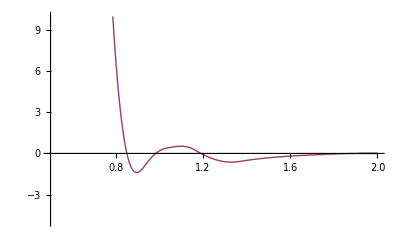

```mathematica
Plot[{
V[a0 r,Akn],
V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk]
},{r,0.5,2},PlotRange->{-5,10},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,b Bk/.sol]  (* set rhoMax sufficiently beyond this value *)
rhoMax=50000;
drho=5//N;
```

2838.23

```mathematica
pair=Table[{r,V[r,a Ak]/.sol},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,b Bk]/.sol},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
```

```mathematica
emb//Length
```

10001

```mathematica
Export[str<>"/"<>str<>"_Vitek_lowT_own_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_lowT_own_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_lowT_own_emb",emb,"Table"]
```

Ru/Ru_Vitek_lowT_own_pair

Ru/Ru_Vitek_lowT_own_rho

Ru/Ru_Vitek_lowT_own_emb

#### Be Vitek Ref. Igarashi, Khantha, and Vitek, Phil. Mag. B 63 (1991) 603

```mathematica
str="Be";
prop=#⟦1⟧&/@Import[str<>"/"<>str<>"_Properties.dat"];
par=Import[str<>"/"<>str<>"_Vitek.dat"]//Flatten;
```

WARNING: modifying embedding function

```mathematica
f[ρ_]:=Sqrt[ρ](1+A ρ)  (* Ref. Vitek Eq (8) *)
```

```mathematica
{a0,cBya,Ec,Ev,σ11,σ33,C11,C12,C13,C33,C44,C66}=prop;

Rak=a0 par⟦1;;7⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Ak=par⟦8;;14⟧;
Rbk=a0 par⟦15;;19⟧+10^-7; (* to avoid HeavisideTheta[0] *)
Bk=par⟦20;;24⟧;
A=par⟦25⟧;

ρ0=1/(2A); (* Ref. Vitek text following Eq. (8) *)
cell=hcpCell[a0,cBya];
basis=hcpCoordsRel;
Ω=cell⟦1⟧×cell⟦2⟧.cell⟦3⟧/Length[basis];
radius=2a0; (* cutoff radius for neighbors in units of a0 *)
R=neighborsList[cell,basis,1,radius];
n=Length[R];
nR=Norm/@R;
```

```mathematica
(* CHECK *)
(* (reference,calculated)  *)
{Ev,Evacancy[Ak,Bk]}
{Ec,Ecohesion[Ak,Bk]}
{ρ0,ρ[Bk]}
{σ11,σhcp[1,1,Ak,Bk]}
{σ33,σhcp[3,3,Ak,Bk]}
{C11,Chcp[1,1,Ak,Bk]}
{C12,Chcp[1,2,Ak,Bk]}
{C13,Chcp[1,3,Ak,Bk]}
{C33,Chcp[3,3,Ak,Bk]}
{C44,Chcp[4,4,Ak,Bk]}
{C66,Chcp[6,6,Ak,Bk]}
{True,(3ρ[Bk])^-1<A<ρ[Bk]^-1}  (* Ref Vitek text following Eq. (8) *)
```

{1.11,1.10115}

{3.32,3.31457}

{78.2573,78.1266}

{0,0.000310426}

{0,-0.00315154}

{1.8687,1.71269}

{0.1723,0.128096}

{0.0687,0.0947092}

{2.1358,2.20315}

{1.0373,1.05029}

{0.8482,0.792298}

{True,True}

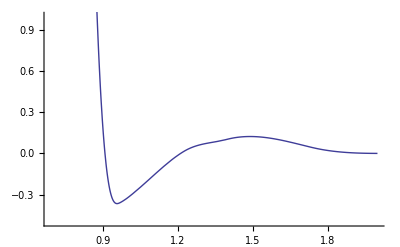

```mathematica
Show[Plot[V[a0 r ,Ak]-2 Dρ[Bk]Φ[a0 r,Bk],{r,0.5,2}],PlotRange->{-.5,1},AxesOrigin->{.5,0}]
```

```mathematica
dr=5 10^-4//N; (* Angstrom *)
nRSmallALat=Norm/@neighborsList[hcpCell[0.8a0,cBya],basis,1,radius];
∑_(j=1)^n Φ[nRSmallALat⟦j⟧,Bk]  (* set rhoMax sufficiently beyond this value *)
rhoMax=1500;
drho=10^-1//N;
```

639.625

```mathematica
pair=Table[{r,V[r,Ak]},{r,0,2a0,dr}];
rho=Table[{r,Φ[r,Bk]},{r,0,2a0,dr}];
emb=Table[{ρ,-f[ρ]},{ρ,0,rhoMax,drho}];
pair//Length
rho//Length
emb//Length
```

9145

9145

15001

```mathematica
Export[str<>"/"<>str<>"_Vitek_pair",pair,"Table"]
Export[str<>"/"<>str<>"_Vitek_rho",rho,"Table"]
Export[str<>"/"<>str<>"_Vitek_emb",emb,"Table"]
```

Be/Be_Vitek_pair

Be/Be_Vitek_rho

Be/Be_Vitek_emb